```mathematica
(*把HH模型降维到二维,Morris-Lecar model*)
Clear["Global`*"]
```

## 1、模型建立

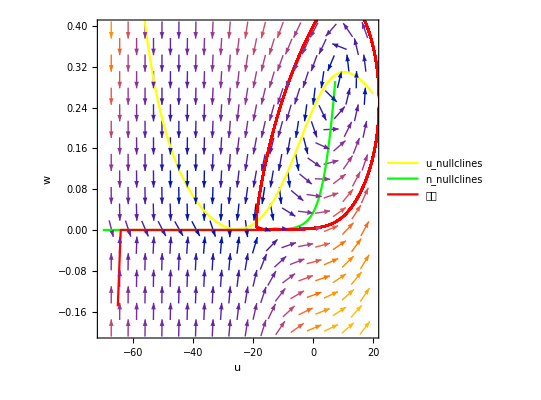

C:\Users\Administrator\Desktop\西电学习资料\Neuronal Dynamics阅读笔记\Chapter1\降维到二维\Is=33.3MLHopf分叉相图.pdf

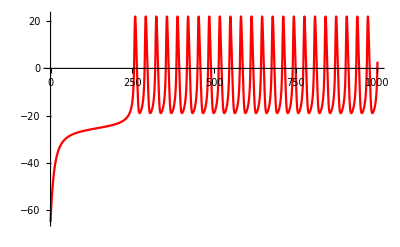

C:\Users\Administrator\Desktop\西电学习资料\Neuronal Dynamics阅读笔记\Chapter1\降维到二维\Is=33.3MLHopf分叉电压.pdf

```mathematica
gna = 4.;(*mS/cm^2*)
u3 = 10.;(*mv*)
u4 = 6.;(*mv*)
una = 100.;(*mv*)
uk = -70.;(*mv*)
ul = -50.;(*mv*)
gk = 8.;(*mS/cm^2*)
gl = 2.;(*mS/cm^2*)
u1 = 0.;(*mv*)
u2 = 15.;(*mv*)
CM = 20.;(*uF/cm^2*)
Is = 33.3;(*uA*)
(*模型微分表达式*)
minfty = 0.5*(1. + Tanh[(u - u1)/u2]);
ninfty = 0.5*(1. + Tanh[(u - u3)/u4]);
ϕ = 0.1*Cosh[(u - u3)/(2.*u4)];
du = (-gna*minfty*(u - una) - gk*n*(u - uk) - gl*(u - ul) + Is)/CM;
dn = ϕ*(ninfty - n);
(*nullclines零斜率线*)
lineu = (-gna*minfty*(u - una) - gl*(u - ul) + Is)/(gk*(u - uk));
linen = ninfty;
(*相图*)
vp = VectorPlot[{du, dn}, {u, -70, 20}, {n, -0.2, 0.4}, PlotRange -> All];
up = Plot[lineu, {u, -70, 20},PlotStyle->{Yellow},PlotLegends->{"u_nullclines",LabelStyle->{FontFamily->"Times New Roman"}}];
np = Plot[linen, {u, -70, 20},PlotStyle->{Green},PlotLegends->{n_nullclines,LabelStyle->{FontFamily->"Times New Roman"}}];
sol = NDSolve[{u'[t] == (-gna*0.5*(1 + Tanh[(u[t] - u1)/u2])*(u[t] - una) - gk*n[t]*(u[t] - uk) - gl*(u[t] - ul) + Is)/CM, n'[t] == 0.1*Cosh[(u[t] - u3)/(2*u4)]*(0.5*(1 + Tanh[(u[t] - u3)/u4]) - n[t]), u[0] == -65, n[0] == -0.15}, {u, n}, {t, 0, 1000}];
pp = ParametricPlot[{u[t], n[t]} /. First@sol // Evaluate, {t, 0, 1000}, PlotRange -> All, PerformanceGoal -> "Quality", PlotStyle -> {Red},PlotLegends->{"轨迹",FontFamily->"Times New Roman"}];
ans=Show[{vp, up, np, pp},Frame->True,FrameLabel->{"u","w"},LabelStyle->{FontFamily->"Times New Roman"}]
Export["C:\\Users\\Administrator\\Desktop\\西电学习资料\\Neuronal Dynamics阅读笔记\\Chapter1\\降维到二维\\Is=33.3MLHopf分叉相图.pdf",ans]
sol = NDSolve[{u'[t] == (-gna*0.5*(1 + Tanh[(u[t] - u1)/u2])*(u[t] - una) - gk*n[t]*(u[t] - uk) - gl*(u[t] - ul) + Is)/CM, n'[t] == 0.1*Cosh[(u[t] - u3)/(2*u4)]*(0.5*(1 + Tanh[(u[t] - u3)/u4]) - n[t]), u[0] == -65, n[0] == -0.15}, u, {t, 0, 1000}];
ans=Plot[u[t] /. First@sol, {t, 0, 1000},PlotRange->All, PlotStyle -> {Red}]
Export["C:\\Users\\Administrator\\Desktop\\西电学习资料\\Neuronal Dynamics阅读笔记\\Chapter1\\降维到二维\\Is=33.3MLHopf分叉电压.pdf",ans]
```

## 2、求解鞍点

```mathematica
(*计算u_nullclines和w_nullclines的交点*)
root=NSolve[{n-lineu==0.,n-linen==0.,-65<u<20,-1<n<1},{u,n}];
F=du/.{u->v+root⟦All,1,2⟧,n->w+root⟦All,2,2⟧};
G=dn/.{u->v+root⟦All,1,2⟧,n->w+root⟦All,2,2⟧};
dFv=D[F,v]/.{v->0.000000001,w->0.000000001};
dFw=D[F,w]/.{v->0.000000001,w->0.000000001};
dGv=D[G,v]/.{v->0.000000001,w->0.000000001};
dGw=D[G,w]/.{v->0.000000001,w->0.000000001};
```

NSolve::ratnz: NSolve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

```mathematica
(*第一个点的特征值，同号的实数，是鞍*)
MatrixForm[M={{dFv⟦1⟧, dFw⟦1⟧},{dGv⟦1⟧, dGw⟦1⟧}}];
Eigenvalues1=Eigenvalues[M]
```

{0.00692297+0.460138 ⅈ,0.00692297-0.460138 ⅈ}

```mathematica
(*第二个点的特征值，不同号的实数，是结*)
MatrixForm[M={{dFv⟦2⟧, dFw⟦2⟧},{dGv⟦2⟧, dGw⟦2⟧}}];
Eigenvalues2=Eigenvalues[M]
```

Part::partw: {0.115983} 的部分 2 不存在.

Part::partw: {-31.0094} 的部分 2 不存在.

Part::partw: {0.00721141} 的部分 2 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

{1/2 ({-0.102137}⟦2⟧+{0.115983}⟦2⟧-√(({-0.102137}⟦2⟧)^2+4 {-31.0094}⟦2⟧ {0.00721141}⟦2⟧-2 {-0.102137}⟦2⟧ {0.115983}⟦2⟧+({0.115983}⟦2⟧)^2)),1/2 ({-0.102137}⟦2⟧+{0.115983}⟦2⟧+√(({-0.102137}⟦2⟧)^2+4 {-31.0094}⟦2⟧ {0.00721141}⟦2⟧-2 {-0.102137}⟦2⟧ {0.115983}⟦2⟧+({0.115983}⟦2⟧)^2))}

```mathematica
(*第三个点的特征值，共轭的虚数，周期性震荡点*)
MatrixForm[M={{dFv⟦3⟧, dFw⟦3⟧},{dGv⟦3⟧, dGw⟦3⟧}}];
Eigenvalues3=Eigenvalues[M]
```

Part::partw: {0.115983} 的部分 3 不存在.

Part::partw: {-31.0094} 的部分 3 不存在.

Part::partw: {0.00721141} 的部分 3 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

{1/2 ({-0.102137}⟦3⟧+{0.115983}⟦3⟧-√(({-0.102137}⟦3⟧)^2+4 {-31.0094}⟦3⟧ {0.00721141}⟦3⟧-2 {-0.102137}⟦3⟧ {0.115983}⟦3⟧+({0.115983}⟦3⟧)^2)),1/2 ({-0.102137}⟦3⟧+{0.115983}⟦3⟧+√(({-0.102137}⟦3⟧)^2+4 {-31.0094}⟦3⟧ {0.00721141}⟦3⟧-2 {-0.102137}⟦3⟧ {0.115983}⟦3⟧+({0.115983}⟦3⟧)^2))}

{1/2 ({-0.102369}⟦3⟧+{0.193209}⟦3⟧-√(({-0.102369}⟦3⟧)^2+4 {-30.262}⟦3⟧ {0.00426194}⟦3⟧-2 {-0.102369}⟦3⟧ {0.193209}⟦3⟧+({0.193209}⟦3⟧)^2)),1/2 ({-0.102369}⟦3⟧+{0.193209}⟦3⟧+√(({-0.102369}⟦3⟧)^2+4 {-30.262}⟦3⟧ {0.00426194}⟦3⟧-2 {-0.102369}⟦3⟧ {0.193209}⟦3⟧+({0.193209}⟦3⟧)^2))}

## 3、分析Ι型特性

增加电流，u_nullclines曲线会往上移，直到左边两个平衡点消失，通过修改Is，可以发现它的特性，具体就是修改上面代码的电流，下面做记录。
1、Is=20，有三个平衡点，其特征值如下，有一个鞍点，一个结，一个震荡点
{-0.565277,-0.0794875}，{-0.179781,0.166154}，{0.0628684+0.306499 ⅈ,0.0628684-0.306499 ⅈ}
2、Is=33.1，有两个平衡点，左边的鞍点和结融合成了一个鞍点，右边有一个震荡点
{-0.296836,-0.00248087}，{0.0459214+0.326764 ⅈ,0.0459214-0.326764 ⅈ}
3、Is>33.1，此时只有右边的一个震荡点了，并且膜电压开始了周期性震荡。
{0.0454199+0.327312 ⅈ,0.0454199-0.327312 ⅈ}

当Is>临界点33.1后，膜电压开始周期性震荡，并且震荡频率随电流的变化是连续的，称为Ι型特性。

## 4、分析二型特性

观察图像可以发现，相图的震荡总是经过曾经鞍点的位置绕一圈回来，尽管鞍点已经消失，但是仍然留下了一片梯度很小的区域，从而使发射速率变得缓慢，表现出I型特性。我们修改参数，使w参数变化快些，或者是使u参数变化慢些，使震荡轨迹经过结点绕一圈，观察现象。我们改变CM=30。

可以发现，在Is=33.1时，由于存在鞍点，没有发射脉冲。但是当Is=33.2时，立马发射了5个脉冲，震荡频率与电流的变化是不连续的，存在一个阶跃点，这种膜特性称为II型特性。